```mathematica
<<Local`QFTToolKit2`
tuItalics
```

Thu 6 Dec 2018 14:39:17

```mathematica
expandDC[sub_:{},scalar_:{},func_:{}]:=tuRepeat[{sub,tuOpDistribute[dotOps],tuOpSimplify[dotOps,scalar]},{func}]
normalize[EXP_List]:=Module[{},EXP/Sqrt[Tr[EXP.EXP]]]
```

Example of entanglement entropy calculation for 2 particle state vector with phase difference on the -- state. 

Taken from URL[https://arxiv.org/abs/1812.01542v1]
————————————————————————————————————————————————————————————
Non-perturbed state |ψ⟩→(|-⟩+|+⟩)/(√2)⊗(|-⟩+|+⟩)/(√2)
→ |ψ⟩→1/2 (|-⟩⊗|-⟩+|-⟩⊗|+⟩+|+⟩⊗|-⟩+|+⟩⊗|+⟩)
With perturbation|ψ⟩→1/2 (ⅇ^(ⅈ δϕ) |-⟩⊗|-⟩+|-⟩⊗|+⟩+|+⟩⊗|-⟩+|+⟩⊗|+⟩)
Entanglement entropy defined I→-Tr[ρ Log[ρ]]
Where density matrix is defined ρ→Tr_b[|ψ⟩·⟨ψ|]
→ 
→ ρ→1/4 ∑[2 |-⟩·⟨-|
(1+ⅇ^(ⅈ δϕ)) |-⟩·⟨+|
|+⟩·⟨-|
ⅇ^(-ⅈ δϕ) |+⟩·⟨-|
2 |+⟩·⟨+|]
Define matrix representation {|-⟩·⟨-|→(0 | 0
0 | 1),|+⟩·⟨+|→(1 | 0
0 | 0),|-⟩·⟨+|→(0 | 1
0 | 0),|+⟩·⟨-|→(0 | 0
1 | 0)}
Compute Eigenvalues ρ→1/2-1/4 ⅇ^(-ⅈ δϕ) √(ⅇ^(ⅈ δϕ) (1+ⅇ^(ⅈ δϕ))^2)
1/4 (2+ⅇ^(-ⅈ δϕ) √(ⅇ^(ⅈ δϕ) (1+ⅇ^(ⅈ δϕ))^2))
→ Log[ρ]→{Log[1/2-1/4 ⅇ^(-ⅈ δϕ) √(ⅇ^(ⅈ δϕ) (1+ⅇ^(ⅈ δϕ))^2)],Log[1/4 (2+ⅇ^(-ⅈ δϕ) √(ⅇ^(ⅈ δϕ) (1+ⅇ^(ⅈ δϕ))^2))]}
⇒ I→-Tr[ρ Log[ρ]]
→ I→∑[-(1/2-1/4 ⅇ^(-ⅈ δϕ) √(ⅇ^(ⅈ δϕ) (1+ⅇ^(ⅈ δϕ))^2)) Log[1/2-1/4 ⅇ^(-ⅈ δϕ) √(ⅇ^(ⅈ δϕ) (1+ⅇ^(ⅈ δϕ))^2)]
-1/4 (2+ⅇ^(-ⅈ δϕ) √(ⅇ^(ⅈ δϕ) (1+ⅇ^(ⅈ δϕ))^2)) Log[1/4 (2+ⅇ^(-ⅈ δϕ) √(ⅇ^(ⅈ δϕ) (1+ⅇ^(ⅈ δϕ))^2))]]

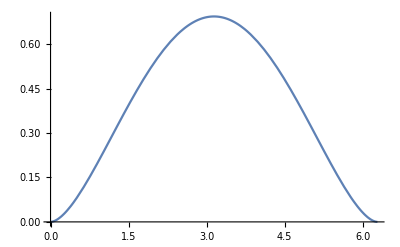

```mathematica
PR["Example of entanglement entropy calculation for 2 particle state vector with phase difference on the -- state. 

Taken from ",
tuArXiv["1812.01542v1"],

line,NL,"Non-perturbed state ",

$=Ket[ψ]->(Ket["+"]+Ket["-"])/Sqrt[2]⊗(Ket["+"]+Ket["-"])/Sqrt[2],
Yield,
$=$//tuOpDistributeF[CircleTimes]//tuOpSimplifyF[CircleTimes]//Simplify,
NL,"With perturbation",
$1=$=$/.kk:Ket["-"]⊗Ket["-"] ->kk Exp[I δϕ],
NL,"Entanglement entropy defined ",
$i=iI->-Tr[ρ Log[ρ]],
NL,"Where density matrix is defined ",
$r=ρ->Subscript[Tr, b][Ket[ψ]·Bra[ψ]],
Yield,
$r=$r/.$/.($1/.(c_:1 )Ket[a_]⊗Ket[b_]->cc[c]Bra[a]⊗Bra[b]/.Ket[ψ]->Bra[ψ]/.cc[δϕ]->δϕ)//expandDC[{},{Exp[_]}];$r//ColumnSumExp;
Yield,
$r=$r/.a_⊗Ket[b_]· c_⊗Bra[d_]:>0/;b=!=d;$r//ColumnSumExp;
$=$r;$//ColumnSumExp;

$=$//tuCircleTimesGather[]//tuOpDistributeF[CircleTimes]//tuOpSimplifyF[CircleTimes,{Exp[_]}]//Simplify;$//ColumnSumExp;
$=$/. (a_⊗(Ket[c_]·Bra[c_]):>a)/.Subscript[Tr, b][a_]->a//Simplify;$//ColumnSumExp,
NL,"Define matrix representation ",
$s={Ket["-"]·Bra["-"]->{{0,0},{0,1}},
Ket["+"]·Bra["+"]->{{1,0},{0,0}},
Ket["-"]·Bra["+"]->{{0,1},{0,0}},
Ket["+"]·Bra["-"]->{{0,0},{1,0}}};$s//MatrixForms,
$=$/.$s;$//MatrixForms;
NL,"Compute Eigenvalues ",
$[[2]]=$[[2]]//Eigenvalues//FullSimplify;
$//ColumnForms,
Yield,$l=$;$l=Log/@$l,
$={$,$l}//tuRuleTimes;
$=Tr/@$;
Imply,$i,
Yield,$1=$=$i/.$;
$//ColumnSumExp
]
Plot[$1[[2]],{δϕ,0,2π}]
```